# Modelos del Flujo de Muones

Referencia para leer sobre los modelos existentes del flujo de muones al nivel del mar.
→
 REF:  Su, N., Liu, Y., Wang, L., Wu, B., & Cheng, J. (2021). A comparison of muon flux models at sea level for muon imaging and low background experiments. Front. Energy Res., 9, 750159.

## Parametrización de Flujo cósmico de muones

#### Fórmula de Gaisser sin el Cos(θ), sin la correción esferica. Con E_µ>>ϵ_µ,ϵ_µ=1GeV y θ < 60°

con A_G=0.14, γ = 2.7, ϵ_π=115/1.1 GeV, ϵ_κ=810/1.1 GeV, B_G= 0.053

```mathematica
f[Emu_,θ_]:=0.14*(Emu)^-2.7*{1/(1+(1.1Emu*Cos[θ Degree])/115)+0.054/(1+(1.1Emu*Cos[θ Degree])/850)}
```

Gráfica de escala lineal, para θ = 0°

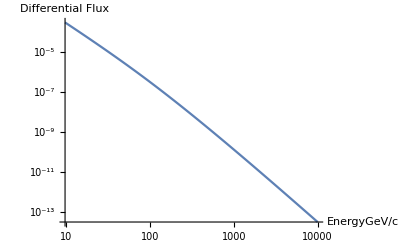

```mathematica
LogLogPlot[f[Emu,0],{Emu,0,10000},AxesLabel->{Text["EnergyGeV/c"],Text["Differential Flux"]}]
```

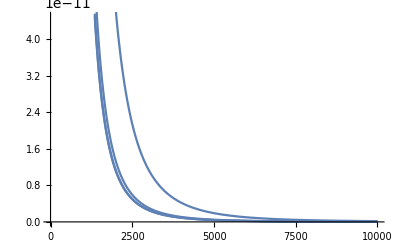

```mathematica
θ1=Plot[f[Emu,0],{Emu,0,10000}];
θ2=Plot[f[Emu,10],{Emu,0,10000}];
θ3=Plot[f[Emu,35],{Emu,0,10000}];
θ4=Plot[f[Emu,80],{Emu,0,10000}];
Show[θ1,θ2,θ3,θ4]
```

Gráfica con escala logarítmica en y ->  que es el flujo diferencial; x -> la energía.

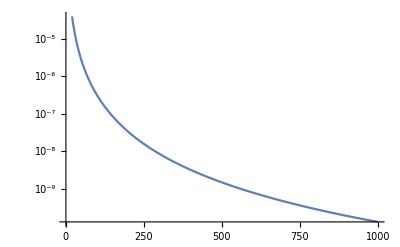

```mathematica
LogPlot[f[Emu,0],{Emu,1,1000}]
```

Gráfica con escala logarítmica en, x -> la energía ; y -> que es el flujo diferencial.

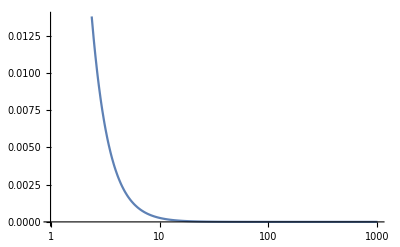

```mathematica
LogLinearPlot[f[Emu,0],{Emu,1,1000}]
```

Gráfica con escala logarítmica en x - y .

```mathematica
Log
```

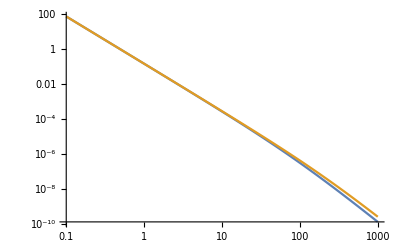

```mathematica
LogLogPlot[{f[Emu,0],f[Emu,65]},{Emu,0.1,1000}]
```

Fórmula de Gaisser-Tang con el Cos (θ), de la correción esferica .

```mathematica
p1=0.102573; p2=-0.068287;p3=0.958633;p4=0.0407253;p5=0.817285;
```

```mathematica
Cosθ[θ_]:=Sqrt[(Cos[θ ]^2+p1^2+p2 Cos[θ ]^p3+p4 Cos[θ ]^p5)/(1+p1^2+p2+p4)];
```

```mathematica
Emu2[Emu_,θ_]:= Emu*(1+(3.64 (*GeV*))/(Emu  Cosθ[θ *π/180]^1.29));
```

```mathematica
FlujoMu[Emu_,θ_]:=0.14 (Emu2[Emu,θ]/(1(*GeV*)))^-2.7*(1/(1+(1.1* Emu *Cosθ[θ *π/180])/(115 (*GeV*)))+0.054/(1+(1.1* Emu *Cosθ[θ *π/180])/(850(*GeV*))))
```

Para 0 ° y 75 ° grados . De 1 GeV a 600 GeV

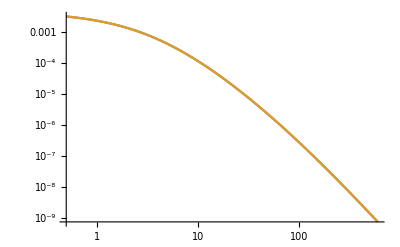

```mathematica
LogLogPlot[{FlujoMu[Emu,0],FlujoMu[Emu,75]},{Emu,0.5,600},GridLines->Automatic,PlotRange->All]
```

```mathematica
REFs. -> [Bonomi, "Applications of cosmic-ray ... "]
-> [Bonechi, "Atmospheric Muons ... "]
-> [Alexandrov, "Muon radiography method ... "]
```